```mathematica
u[r_,z_]= (1-r^2/a^2)(1-z/L)
```

(1-r^2/a^2) (1-z/L)

```mathematica
ψ[l_,n_,r_,z_]=Sin[l Pi z/L] BesselJ[0,j[n] r/a]
```

BesselJ[0,(r j[n])/a] Sin[(l π z)/L]

```mathematica
j[n_]:= (BesselJZero[0,n]//N)/; n∈Integers
```

```mathematica
λ[l_,n_]= -l^2 Pi^2/L^2 -j[n]^2/a^2
```

-(l^2 π^2)/L^2-j[n]^2/a^2

```mathematica
ρbar[r_,z_]= 4/a^2(1-z/L);
```

```mathematica
c[l_,n_]= Integrate[ψ[l,n,r,z]ρbar[r,z] r,{r,0,a},{z,0,L}]/Integrate[ψ[l,n,r,z]^2 r,{r,0,a},{z,0,L}]
```

-(32 BesselJ[1,j[n]] (l π-Sin[l π]))/(a^2 l π (BesselJ[0,j[n]]^2+BesselJ[1,j[n]]^2) j[n] (-2 l π+Sin[2 l π]))

```mathematica
Δϕ[r_,z_]= Sum [c[l,n]ψ[l,n,r,z]/λ[l,n],{l,1,10},{n,1,10}]
```

-0.494437 BesselJ[0,2.40483 r] Sin[(π z)/2]+0.0823193 BesselJ[0,5.52008 r] Sin[(π z)/2]-0.0280278 BesselJ[0,8.65373 r] Sin[(π z)/2]+0.0131302 BesselJ[0,11.7915 r] Sin[(π z)/2]-0.00732677 BesselJ[0,14.9309 r] Sin[(π z)/2]+0.00456267 BesselJ[0,18.0711 r] Sin[(π z)/2]-0.00306309 BesselJ[0,21.2116 r] Sin[(π z)/2]+0.00217182 BesselJ[0,24.3525 r] Sin[(π z)/2]-0.00160511 BesselJ[0,27.4935 r] Sin[(π z)/2]+0.00122555 BesselJ[0,30.6346 r] Sin[(π z)/2]-0.130309 BesselJ[0,2.40483 r] Sin[π z]+0.0336072 BesselJ[0,5.52008 r] Sin[π z]-0.01279 BesselJ[0,8.65373 r] Sin[π z]+0.00623876 BesselJ[0,11.7915 r] Sin[π z]-0.0035469 BesselJ[0,14.9309 r] Sin[π z]+0.00223114 BesselJ[0,18.0711 r] Sin[π z]-0.00150689 BesselJ[0,21.2116 r] Sin[π z]+0.00107258 BesselJ[0,24.3525 r] Sin[π z]-0.000794797 BesselJ[0,27.4935 r] Sin[π z]+0.000607991 BesselJ[0,30.6346 r] Sin[π z]-0.0485819 BesselJ[0,2.40483 r] Sin[(3 π z)/2]+0.0171577 BesselJ[0,5.52008 r] Sin[(3 π z)/2]-0.00744323 BesselJ[0,8.65373 r] Sin[(3 π z)/2]+0.00384096 BesselJ[0,11.7915 r] Sin[(3 π z)/2]-0.0022456 BesselJ[0,14.9309 r] Sin[(3 π z)/2]+0.00143481 BesselJ[0,18.0711 r] Sin[(3 π z)/2]-0.000978342 BesselJ[0,21.2116 r] Sin[(3 π z)/2]+0.000700713 BesselJ[0,24.3525 r] Sin[(3 π z)/2]-0.000521463 BesselJ[0,27.4935 r] Sin[(3 π z)/2]+0.000400122 BesselJ[0,30.6346 r] Sin[(3 π z)/2]-0.0225323 BesselJ[0,2.40483 r] Sin[2 π z]+0.00969086 BesselJ[0,5.52008 r] Sin[2 π z]-0.00473935 BesselJ[0,8.65373 r] Sin[2 π z]+0.00260201 BesselJ[0,11.7915 r] Sin[2 π z]-0.00157335 BesselJ[0,14.9309 r] Sin[2 π z]+0.00102533 BesselJ[0,18.0711 r] Sin[2 π z]-0.000707861 BesselJ[0,21.2116 r] Sin[2 π z]+0.000511185 BesselJ[0,24.3525 r] Sin[2 π z]-0.000382605 BesselJ[0,27.4935 r] Sin[2 π z]+0.000294792 BesselJ[0,30.6346 r] Sin[2 π z]-0.0120928 BesselJ[0,2.40483 r] Sin[(5 π z)/2]+0.00588454 BesselJ[0,5.52008 r] Sin[(5 π z)/2]-0.00317498 BesselJ[0,8.65373 r] Sin[(5 π z)/2]+0.00185131 BesselJ[0,11.7915 r] Sin[(5 π z)/2]-0.00116047 BesselJ[0,14.9309 r] Sin[(5 π z)/2]+0.00077335 BesselJ[0,18.0711 r] Sin[(5 π z)/2]-0.00054171 BesselJ[0,21.2116 r] Sin[(5 π z)/2]+0.000395077 BesselJ[0,24.3525 r] Sin[(5 π z)/2]-0.00029777 BesselJ[0,27.4935 r] Sin[(5 π z)/2]+0.000230597 BesselJ[0,30.6346 r] Sin[(5 π z)/2]-0.00718636 BesselJ[0,2.40483 r] Sin[3 π z]+0.00378813 BesselJ[0,5.52008 r] Sin[3 π z]-0.00220718 BesselJ[0,8.65373 r] Sin[3 π z]+0.001359 BesselJ[0,11.7915 r] Sin[3 π z]-0.000882868 BesselJ[0,14.9309 r] Sin[3 π z]+0.000602349 BesselJ[0,18.0711 r] Sin[3 π z]-0.000428683 BesselJ[0,21.2116 r] Sin[3 π z]+0.000316126 BesselJ[0,24.3525 r] Sin[3 π z]-0.000240169 BesselJ[0,27.4935 r] Sin[3 π z]+0.000187087 BesselJ[0,30.6346 r] Sin[3 π z]-0.00460013 BesselJ[0,2.40483 r] Sin[(7 π z)/2]+0.00255893 BesselJ[0,5.52008 r] Sin[(7 π z)/2]-0.00158192 BesselJ[0,8.65373 r] Sin[(7 π z)/2]+0.00102112 BesselJ[0,11.7915 r] Sin[(7 π z)/2]-0.000686148 BesselJ[0,14.9309 r] Sin[(7 π z)/2]+0.000479289 BesselJ[0,18.0711 r] Sin[(7 π z)/2]-0.000346795 BesselJ[0,21.2116 r] Sin[(7 π z)/2]+0.000258791 BesselJ[0,24.3525 r] Sin[(7 π z)/2]-0.000198328 BesselJ[0,27.4935 r] Sin[(7 π z)/2]+0.000155505 BesselJ[0,30.6346 r] Sin[(7 π z)/2]-0.00311505 BesselJ[0,2.40483 r] Sin[4 π z]+0.00179917 BesselJ[0,5.52008 r] Sin[4 π z]-0.00116412 BesselJ[0,8.65373 r] Sin[4 π z]+0.000782119 BesselJ[0,11.7915 r] Sin[4 π z]-0.000542034 BesselJ[0,14.9309 r] Sin[4 π z]+0.00038734 BesselJ[0,18.0711 r] Sin[4 π z]-0.00028497 BesselJ[0,21.2116 r] Sin[4 π z]+0.000215282 BesselJ[0,24.3525 r] Sin[4 π z]-0.000166508 BesselJ[0,27.4935 r] Sin[4 π z]+0.000131474 BesselJ[0,30.6346 r] Sin[4 π z]-0.00220414 BesselJ[0,2.40483 r] Sin[(9 π z)/2]+0.00130802 BesselJ[0,5.52008 r] Sin[(9 π z)/2]-0.000876796 BesselJ[0,8.65373 r] Sin[(9 π z)/2]+0.000609169 BesselJ[0,11.7915 r] Sin[(9 π z)/2]-0.000434007 BesselJ[0,14.9309 r] Sin[(9 π z)/2]+0.000316868 BesselJ[0,18.0711 r] Sin[(9 π z)/2]-0.000236955 BesselJ[0,21.2116 r] Sin[(9 π z)/2]+0.000181239 BesselJ[0,24.3525 r] Sin[(9 π z)/2]-0.000141512 BesselJ[0,27.4935 r] Sin[(9 π z)/2]+0.000112559 BesselJ[0,30.6346 r] Sin[(9 π z)/2]-0.00161545 BesselJ[0,2.40483 r] Sin[5 π z]+0.000978131 BesselJ[0,5.52008 r] Sin[5 π z]-0.000674094 BesselJ[0,8.65373 r] Sin[5 π z]+0.000481628 BesselJ[0,11.7915 r] Sin[5 π z]-0.000351618 BesselJ[0,14.9309 r] Sin[5 π z]+0.000261861 BesselJ[0,18.0711 r] Sin[5 π z]-0.000198909 BesselJ[0,21.2116 r] Sin[5 π z]+0.000154009 BesselJ[0,24.3525 r] Sin[5 π z]-0.000121405 BesselJ[0,27.4935 r] Sin[5 π z]+0.0000972963 BesselJ[0,30.6346 r] Sin[5 π z]

```mathematica
ϕ[r_,z_]= u[r,z]+Δϕ[r,z];
```

```mathematica
L=2;a=1;
```

```mathematica
ϕ[.1,.2]
```

5.51539

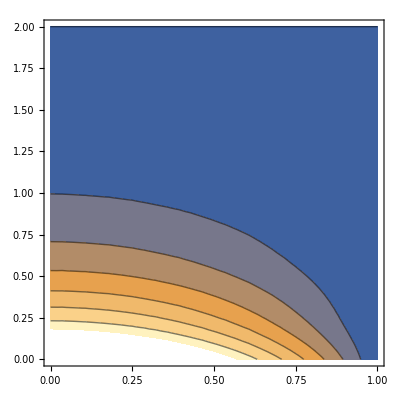

```mathematica
ContourPlot[ϕ[r,z],{r,0,a},{z,0,L}]
```

```mathematica
BesselJ[1/2, r]/Sqrt[r]
```

(√(2/π) Sin[r])/r

```mathematica
BesselJ[-3/2, r]/Sqrt[r]
```

(√(2/π) (-Cos[r]/r-Sin[r]))/r

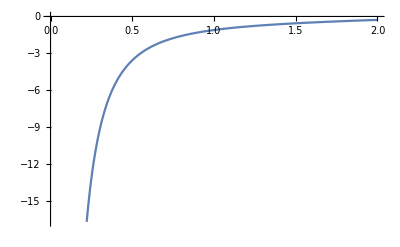

```mathematica
Plot[%,{r,0,2}]
```

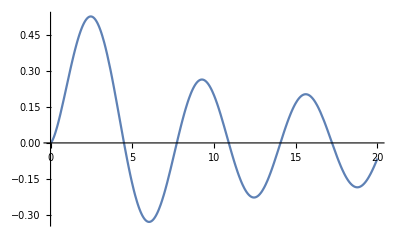

```mathematica
Plot[BesselJ[3/2,r],{r,0,20}]
```

```mathematica
BesselJZero[1/2,2]//N
```

6.28319

```mathematica
BesselJ[3/2,r]
```

(√(2/π) (-Cos[r]+Sin[r]/r))/(√r)

```mathematica
Clear[j]
```

```mathematica
j[l_,n_]:=(j[l,n]=N[BesselJZero[l,n]]//N)/; n∈Integers
```

```mathematica
R[l_,n_,r_]= BesselJ[l+1/2, j[l+1/2,n] r/a]/Sqrt[r]
```

BesselJ[1/2+l,r j[1/2+l,n]]/(√r)

```mathematica
R[0,1,r]
```

(0.450158 (0.+Cos[1.5708-3.14159 r]))/r

```mathematica
a=1;
```

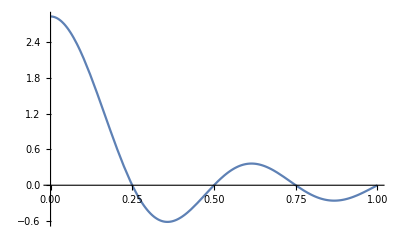

```mathematica
Plot[R[0,4,r],{r,0,1},PlotRange->All]
```

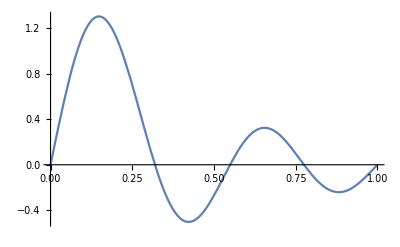

```mathematica
Plot[R[1,4,r],{r,0,1},PlotRange->All]
```

```mathematica
Clear[c]
```

```mathematica
c[n_]:=c[n]= NIntegrate[ r^2 R[1,n,r] 2 Sqrt[Pi/3] r,{r,0,1}]/ (λ[1,n]NIntegrate[ r^2 R[1,n,r]^2,{r,0,1}])
```

```mathematica
λ[1,n_]= -(j[1+1/2,n]/a)^2
```

-j[3/2,n]^2

```mathematica
c[1]
```

-0.122798

```mathematica
c[2]
```

0.0311861

```mathematica
ϕ[r_,θ_]= Sum[c[n] R[1,n,r],{n,1,10}]SphericalHarmonicY[1,0,θ,ϕ]
```

1/2 √(3/π) Cos[θ] ((0.000114408 (Cos[3.14159-32.9564 r]+(0.0303431 Sin[3.14159-32.9564 r])/r))/r-(0.000154583 (Cos[3.14159-29.8116 r]+(0.033544 Sin[3.14159-29.8116 r])/r))/r+(0.000216025 (Cos[3.14159-26.6661 r]+(0.0375009 Sin[3.14159-26.6661 r])/r))/r-(0.000314909 (Cos[3.14159-23.5195 r]+(0.042518 Sin[3.14159-23.5195 r])/r))/r+(0.000484775 (Cos[3.14159-20.3713 r]+(0.0490887 Sin[3.14159-20.3713 r])/r))/r-(0.000802876 (Cos[3.14159-17.2208 r]+(0.0580695 Sin[3.14159-17.2208 r])/r))/r+(0.00147448 (Cos[3.14159-14.0662 r]+(0.0710924 Sin[3.14159-14.0662 r])/r))/r-(0.00317045 (Cos[3.14159-10.9041 r]+(0.0917084 Sin[3.14159-10.9041 r])/r))/r+(0.00895251 (Cos[3.14159-7.72525 r]+(0.129446 Sin[3.14159-7.72525 r])/r))/r-(0.0462214 (Cos[3.14159-4.49341 r]+(0.222548 Sin[3.14159-4.49341 r])/r))/r)

```mathematica
ParametricPlot3D[{r Sin[θ], r Cos[θ],ϕ[r,θ]},{r,0,a},{θ,0,Pi},BoxRatios->{1,2,1}]
```

-Graphics3D-